# Confluence in Multiway Cellular Automata

## Singleway and Multiway Cellular Automata

In a cellular automaton (CA), collections of colored cells are built up by applying rules to each block of cells to find the color of every cell in the next step. The simplest case of this is called an elementary CA, with a row of black and white cells for every step and rules based on the colors of a cell and its two nearest neighbors. Despite their simplicity, elementary CA’s are capable of producing complex behavior. A multiway CA is a modification of this system where only one color replacement from the rule is applied at one position each step. This is the behavior of elementary rule 110 as a singleway and multiway system:

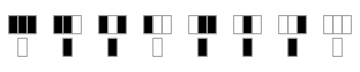
-Graphics--Graphics-
-Graphics-Left: Singleway behavior of rule 110 from a random initial condition
Right: Multiway state transitions of rule 110 from all initial conditions of five cells
Bottom: Plot of cell replacements corresponding to rule 110

```mathematica
multi=ResourceFunction["MultiwaySystem"];
render="StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->30],#1,#3]&);
statesGraph=multi[CellularAutomaton[110],Tuples[{0,1},5],1,"StatesGraph",render,ImageSize->{300,300}];
Labeled[Column[{Row[{
ArrayPlot[CellularAutomaton[110,RandomInteger[1,200],200],ImageSize->{300,300}],statesGraph
}],
RulePlot[CellularAutomaton@110,ImageSize->Medium]},Alignment->Center],
Text["Left: Singleway behavior of rule 110 from a random initial condition
Right: Multiway state transitions of rule 110 from all initial conditions of five cells
Bottom: Plot of cell replacements corresponding to rule 110"]]
```

Multiway CA’s can also be visualized by constructing singleway CA plots from different possible paths through the multiway system. This shows a sample of the possible paths through the states graph above starting from the single black cell initial condition:

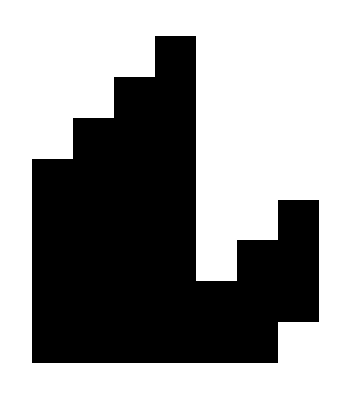
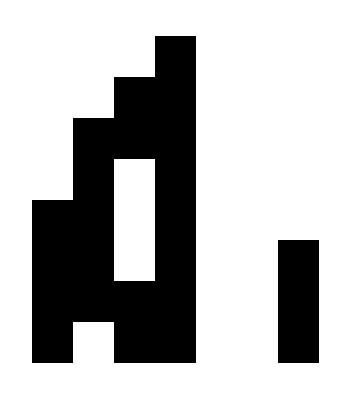
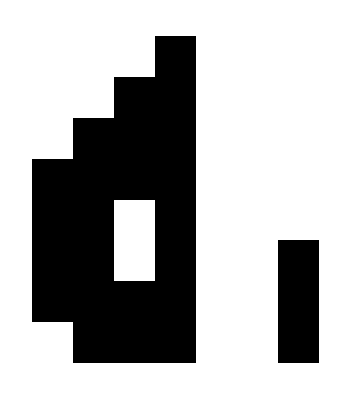
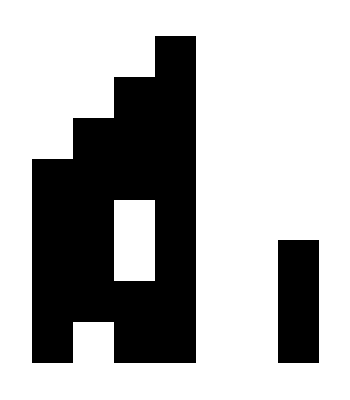
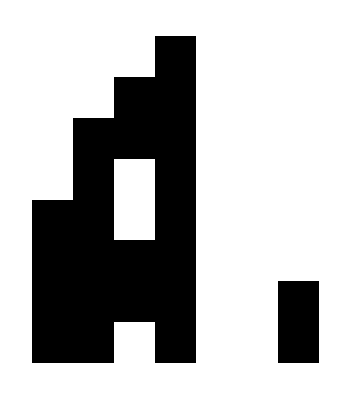
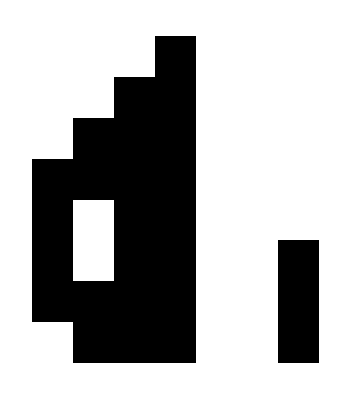
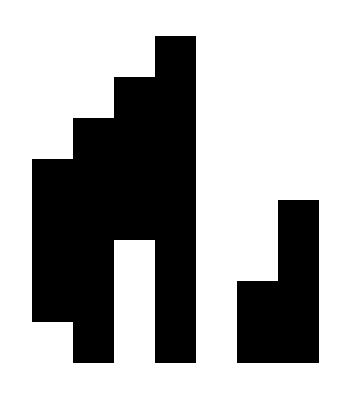

```mathematica
getAllPathsFromState[graph_,start_,length_]:=
	Flatten[FindPath[graph,start,#,length,All]&/@Rest[VertexOutComponent[graph,start]],1]
getAllPathsToState[graph_,finish_,length_]:=
	Flatten[FindPath[graph,#,finish,length,All]&/@Rest[VertexInComponent[graph,finish]],1]
overlayPaths[paths_]:=ArrayPlot[N@Total[paths]/Length[paths],ImageSize->Small]
cellStateProbabilities[graph_,init_,length_]:=With[{allPaths=getAllPathsFromState[graph,init,length]},
	Table[N@Mean[#[[i]]&/@Select[allPaths,Length[#]≥i&]],{i,length}]]
graph=multi[CellularAutomaton[110],CenterArray[1,7],7,"StatesGraph",render,ImageSize->Medium];
paths=getAllPathsFromState[graph,CenterArray[1,7],{7}];
Row[ArrayPlot[#,ImageSize->Tiny]&/@RandomSample[paths,7]]
```

It can also be viewed by overlaying these graphs to see the chance of each cell being black or white at different steps:

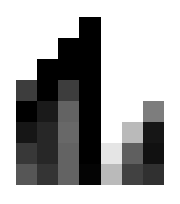

```mathematica
overlayPaths[paths]
```

## Confluence

This project aims to study confluence in multiway CA’s. A graph is confluent when for every node, every branch from the node can always merge back into some common state. I also define total confluence as a graph where every node can always reach every other node, regardless of branching.

```mathematica
confluentQ[graph_] := AllTrue[WeaklyConnectedGraphComponents[graph],
	Function[cc, AnyTrue[VertexList[cc], ContainsExactly[VertexInComponent[cc, #], VertexList[cc]] &]]]

totalConfluentQ[graph_] := CompleteGraphQ[TransitiveClosureGraph[graph]]
```

This is the states graph for rule 110 from every initial condition of five cells. This graph is confluent, as all connected states can always reach one of the states in the central loop, and the all white state is an island which cannot branch and so must be confluent. It is not totally confluent, as the states on the outside can’t be reached from the inside, and the all white state is unconnected:

```mathematica
Row[{multiwayGraph=ResourceFunction["MultiwaySystem"][CellularAutomaton[110],Tuples[{0,1},5],1,"StatesGraph","StateRenderingFunction"->(Inset[ArrayPlot[{#2},ImageSize->25],#1,#3]&),ImageSize->Medium],Column[{Text["Confluent: "<>ToString@confluentQ[multiwayGraph]],Text["Total Confluent: "<>ToString@totalConfluentQ[multiwayGraph]]}]},"\t"]
```

-Graphics-Confluent: True
Total Confluent: False

I call the states which every other state in the same piece of the graph can always reach confluent end states. In this case, the confluent end states are the central connected portion of the graph, as well as the island of all white cells:

```mathematica
getConfluentEndStates[graph_]:=Function[cc,Select[VertexList[cc],
	ContainsExactly[VertexInComponent[cc,#],VertexList[cc]]&]]/@WeaklyConnectedGraphComponents[graph]
```

```mathematica
Row[ArrayPlot[{#},ImageSize->50]&/@Flatten[getConfluentEndStates[multiwayGraph],1]," "]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

## Conclusions

I found that most multiway elementary CA rules are confluent, but that confluence depends on the width of the cell rows as well as the rule. Only a few multiway CA’s were totally confluent. Confluence of one rule can fluctuate based on row width in a variety of ways. The behavior of multiway CA’s seem to be somewhat related to that of their singleway counterparts, but with a very limited sample size I did not find a correlation between the behavior class of a singleway CA and the confluence of its corresponding multiway CA.

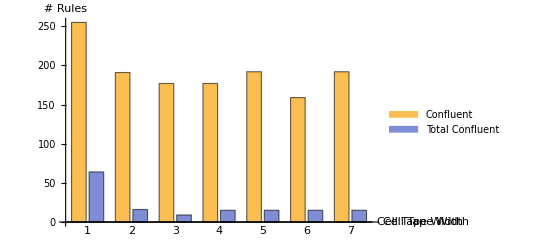

```mathematica
getAllElementaryGraphs[maxCells_]:=
	Table[multi[CellularAutomaton[i],Tuples[{0,1},j],1,"StatesGraphStructure"],{i,255},{j,maxCells}];
getConfluenceByCells[allGraphs_]:=Transpose@Map[confluentQ,allGraphs,{2}]
getTotalConfluenceByCells[allGraphs_]:=Transpose@Map[totalConfluentQ,allGraphs,{2}]
getConfluenceCountsByCells[confluenceByCells_]:=
	Table[Count[confluenceByCells[[i]],True],{i,Length@confluenceByCells}]
getBothConfluenceCounts[allGraphs_]:=With[{
	confluenceCountsByCells=getConfluenceCountsByCells[getConfluenceByCells[allGraphs]],
	totalConfluenceCountsByCells=getConfluenceCountsByCells[getTotalConfluenceByCells[allGraphs]]},
	Table[{confluenceCountsByCells[[i]],totalConfluenceCountsByCells[[i]]},{i,Length@confluenceCountsByCells}]]
BarChart[getBothConfluenceCounts[getAllElementaryGraphs[7]],ChartLabels->{Placed[Range[10],Below],None},AxesLabel->{Text["Cell Tape Width"],"# Rules"},ChartLegends->{"Confluent","Total Confluent"}]
```

Confluence can be an important property to define how a multiway system can be viewed as a computation, with confluent end states being possible results of the computation. It may also be related to the universality of a multiway system. The description and measure of confluence from this project can also be applied to all types of multiway systems, not just CA's.

## Future Work

I would like to study the relationship between confluence of a multiway CA and the behavior of its singleway counterpart in more detail, and study the multiway behavior of more classes of singleway CA rules. An extension of this project would be to study causal invariance in these systems and its relationship to confluence, and extending the definition of causal invariance to non-terminating systems. Finally, I’d like to study universality in multiway systems. This is not yet a well-defined concept, but some of my intuition from this project is leading me towards a solution based on correlations in the causal graphs of different systems.

## Acknowledgements

I would like to thank my mentor Christopher Wolfram for guiding me and helping me turn ideas into code, Stephen Wolfram for providing the project and pushing me to understand multiway systems at a deeper level, Jonathan Gorard and Max Piskunov for their contributions to the MultiwaySystem repository function, and all the administrators at the summer school for making this experience possible.